## QNMs of a Schwarzschild Black Hole

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Computing the QNMs

Follows the implementation of the QNM calculation method.

### Set-up

```mathematica
f[r_]:=1-(2 M)/r;V=f[r]((l(l+1))/r^2-(6 M)/r^3);
rs[r_]:=Simplify[Integrate[1/f[r],r],r>0];
EQ=f[r]^2 ψ''[r]+f'[r]f[r]ψ'[r]+(ω^2-V)ψ[r];
```

```mathematica
Print["Tortoise coordinate r_* = ", rs[r]];
Print["Regge-Wheeler equation:\n ", EQ, " = 0"];
```

Tortoise coordinate r_* = r+2 M Log[-2 M+r]

Regge-Wheeler equation:
 (-((-(6 M)/r^3+(l (1+l))/r^2) (1-(2 M)/r))+ω^2) ψ[r]+(2 M (1-(2 M)/r) ψ'[r])/r^2+(1-(2 M)/r)^2 ψ''[r] = 0

### Expansion at the horizon

The goal of this Section is to compute an approximate solution near the event horizon.
The black hole surface is totally absorbing, hence at the horizon we require ingoing waves only:
	ψ ∼ e^(-ⅈω r_*)
where r_* is the tortoise coordinate. We multiply for a function of r and expand it as series of powers around the horizon:
	ψ∼e^(-ⅈω r_*)h(r) = (e^(-ⅈω r)(r-2M))^(-2M ⅈω)h(r)	using the definition of r_*
	h(r) = ∑(h_n(r-2M))^n
Then, we substitute in the master equation and solve for the coefficients h_n.

```mathematica
ϕHor[r_]:=(r-2M)^(-2 M ⅈ ω)h[r];(* the term e^-ⅈωr can be neglected since it doens't go to 0 when r->0 *)
sHor=Simplify[(r-2 M)^(2 M ⅈ ω-1)×EQ/.{ψ[r]->ϕHor[r],ψ'[r]->ϕHor'[r],ψ''[r]->ϕHor''[r]}]
```

((-r (l+l^2-r^2 ω^2)+2 M (3+ⅈ r ω+r^2 ω^2)) h[r]+r (2 (M-2 ⅈ M r ω) h'[r]+r (-2 M+r) h''[r]))/r^4

```mathematica
(*Series coefficients*)
CoefHor[ord_]:=Module[{H,EQ,s},
H[r_]:=Sum[hHor[i](r-2 M)^i,{i,0,ord+5}];
EQ=sHor/.{h[r]->H[r],h'[r]->H'[r],h''[r]->H''[r]};
s=Simplify[Series[EQ,{r,2 M,ord}]];
(*Solve the system*)
Simplify[Solve[Table[SeriesCoefficient[s,i]==0,{i,0,ord}],Table[hHor[i],{i,1,ord+1}]]]
]
```

```mathematica
ordHor=1;(* NOTE: the last coefficient is one order higher *)
CoefHor[ordHor]
```

{(-((-3+l+l^2-2 ⅈ M ω-8 M^2 ω^2) hHor[0])+2 M (1-4 ⅈ M ω) hHor[1])/(8 M^3)==0,(3 (-4+l+l^2-2 ⅈ M ω-4 M^2 ω^2) hHor[0]-2 M (l hHor[1]+l^2 hHor[1]-2 M (5 ⅈ ω hHor[1]+4 M ω^2 hHor[1]+4 hHor[2]-8 ⅈ M ω hHor[2])))/(16 M^4)==0}

```mathematica
ordHor=7;(* NOTE: the last coefficient is one order higher *)
coefHor=CoefHor[ordHor][[1]];
```

```mathematica
Export["CoefHor_Schw_7.m",coefHor]
```

CoefHor_Schw_7.m

### Expansion at infinity

The goal of this Section is to compute an approximate solution at infinity.
At infinity only outgoing waves exist:
	ψ ∼ e^(ⅈω r_*)
We multiply for a function of r and expand it as series of powers around infinity:
	ψ∼e^(ⅈω r_*)g(r)
	g(r)= ∑ g_n r^-n
Then, we substitute in the master equation and solve for the coefficients g_n.

```mathematica
ϕInf[r_]:=Exp[ⅈ ω z[r]]g[r];
s=Simplify[EQ/.{ψ[r]->ϕInf[r],ψ'[r]->ϕInf'[r],ψ''[r]->ϕInf''[r]}];
sInf=Simplify[Exp[-ⅈ ω z[r]]× s/.{z[r]->rs[r],z'[r]->D[rs[r],r],z''[r]->D[rs[r],{r,2}]}]
```

((2 M-r) ((-6 M+l (1+l) r) g[r]+r (-2 (M+ⅈ r^2 ω) g'[r]+(2 M-r) r g''[r])))/r^4

```mathematica
(*Series coefficients*)
CoefInf[ord_]:=Module[{G,EQ,s},
G[r_]:=Sum[gInf[i]/r^i,{i,0,ord+5}];
EQ=sInf/.{g[r]->G[r],g'[r]->G'[r],g''[r]->G''[r]};
s=Simplify[Series[EQ,{r,∞,ord}]];
(*Solve the system*)
Simplify[Solve[Table[SeriesCoefficient[s,i]==0,{i,2,ord}],Table[gInf[i],{i,1,ord-1}]]]
]
```

```mathematica
ordInf=13;(* NOTE: the last coefficient is one order lower *)
coefInf=CoefInf[ordInf][[1]];
```

```mathematica
Export["CoefInf_Schw_13.m",coefInf]
```

CoefInf_Schw_13.m

### QNM finder

We adopt a direct integration method.
First, the master equation is integrated from the horizon and infinity using the limits computed above as boundary conditions. Then, the two results are ‘attached together’ at a match point sufficiently far from both the horizon and infinity.
The QNM is estimated as the value smoothing the final result, i.e. giving a continuous first derivative at the match point. This can be achieved finding the root of a function that compute the difference of the first derivatives of the two results.

```mathematica
coefHor=Import["SeriesCoef/CoefHor_Schw_10.m"];
coefInf=Import["SeriesCoef/CoefInf_Schw_10.m"];
```

```mathematica
(* Integrator V2.5 *)
IntQNM[ω0_,theta_,coefHor_,coefInf_]:=Module[{rules,param,prec,rHor,rm,rInf,ξ,ξHor,ξInf,EQs,BCs,ordHor,ordInf},
rules={AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->20};

param=Union[{M->1,ω->ω0,hHor[0]->1,gInf[0]->1},Thread[{l,eps,match,inf}->theta]];
prec=Max[20,Precision[param]];param=SetPrecision[param,prec];

rHor=2M(1+eps)/.param;
rm=match×M/.param;
rInf=inf×M/.param;

EQs=SetPrecision[{EQ==0}//.Union[param,{ψ[r]->ξ[r],ψ'[r]->ξ'[r],ψ''[r]->ξ''[r]}],prec];

(* Solution integrating from the horizon *)
ordHor=Length[coefHor];
ξHor=(r-2 M)^(-2 M ⅈ ω)Sum[hHor[i](r-2 M)^i,{i,0,ordHor}]//.Union[param,coefHor];
BCs=SetPrecision[{ξ[rHor]==ξHor/.r->rHor,ξ'[rHor]==D[ξHor,r]/.r->rHor},prec];

ψHor=ξ[r]/.NDSolve[Union[EQs,BCs],ξ,{r,rHor,rm},rules][[1]];

(* Solution integration from infinity *)
ordInf=Length[coefInf];
ξInf=Exp[ⅈ ω rs[r]]Sum[gInf[i]/r^i,{i,0,ordInf}]//.Union[param,coefInf];
BCs=SetPrecision[{ξ[rInf]==ξInf/.r->rInf,ξ'[rInf]==D[ξInf,r]/.r->rInf},prec];

ψInf=ξ[r]/.NDSolve[Union[EQs,BCs],ξ,{r,rInf,rm},rules][[1]];

(*Linear combination*)
b=ψHor/ψInf/.r->rm;(* we fix the coefficients of the linear combination in order for ψn to be continuous at r=rm *)
(* ψn=Piecewise[{{ψHor,r<rm},{b×ψInf,r≥rm}}]; *)

Δψp=(D[ψHor,r]-D[b ψInf,r])/D[ψHor,r]/.r->rm;
{Δψp}
]
```

```mathematica
FindQNM[ωguess_,theta_]:=Module[{g,ωroot},
g[x_?NumericQ]:=IntQNM[x,theta,coefHor,coefInf][[1]];
ωroot=x/.FindRoot[g[x]==0,{x,ωguess},AccuracyGoal->6,WorkingPrecision->20][[1]];

Return[{ωroot,Abs[g[ωroot]]}];
]
```

```mathematica
FindQNM[0.4-0.1ⅈ,{2,10^-10,10,50}]
```

{0.37367165587586123622-0.088962275243935302159 ⅈ,8.×10^-16}

### Past integrators

Older versions of the integrator. Main difference is the enforcing of the chosen working precision during the calculation.

```mathematica
(* Integrator V2 *)
IntQNM[ω0_,value_,coefHor_,coefInf_]:=Module[{rules,param,rHor,rm,rInf,ξ,ξHor,ξInf,EQs,BCs,ordHor,ordInf},
rules={AccuracyGoal->12,PrecisionGoal->12,WorkingPrecision->MachinePrecision};
param=Union[{M->1,ω->ω0,hHor[0]->1,gInf[0]->1},Thread[{l,eps,match,inf}->value]];

rHor=2M(1+eps)/.param;
rm=match×M/.param;
rInf=inf×M/.param;

EQs={EQ==0}//.Union[param,{ψ[r]->ξ[r],ψ'[r]->ξ'[r],ψ''[r]->ξ''[r]}];

(* Solution integrating from the horizon *)
ordHor=Length[coefHor];
ξHor=(r-2 M)^(-2 M ⅈ ω)Sum[hHor[i](r-2 M)^i,{i,0,ordHor}]//.Union[param,coefHor];
BCs={ξ[rHor]==ξHor/.r->rHor,ξ'[rHor]==D[ξHor,r]/.r->rHor};
solHor=NDSolve[Union[EQs,BCs],ξ,{r,rHor,rm},rules];
ψHor=ξ[r]/.solHor[[1]];

(* Solution integration from infinity *)
ordInf=Length[coefInf];
ξInf=Exp[ⅈ ω rs[r]]Sum[gInf[i]/r^i,{i,0,ordInf}]//.Union[param,coefInf];
BCs={ξ[rInf]==ξInf/.r->rInf,ξ'[rInf]==D[ξInf,r]/.r->rInf};
solInf=NDSolve[Union[EQs,BCs],ξ,{r,rInf,rm},rules];
ψInf=ξ[r]/.solInf[[1]];

(*Linear combination*)
b=ψHor/ψInf/.r->rm;(* we fix the coefficients of the linear combination in order for ψn to be continuous at r=rm *)
ψn=Piecewise[{{ψHor,r<rm},{b×ψInf,r≥rm}}];
Δψp=(D[ψHor,r]-D[b ψInf,r])/D[ψHor,r]/.r->rm;
{Δψp}
]
```

## Numerical Stability

In this Section the QNM finder is tested against different sets of its hyperparameters. The latter are the ‘integration parameters’ defining numerically the event horizon (ϵ), the point of match (μ) and infinity (ι), and the order at which the series expansion at the horizon and at infinity are truncated.

```mathematica
ωSBH=(0.7473433688360838- 0.1779246313778714ⅈ)/2;(* analytical value of Schwarzschild BH's n=1 QNM *)
ωguess=2/5-1/10 ⅈ;
Print["For a Schwarzschild BH: ω_0 = ", ωSBH, "\nInitial guess: ω_guess = ", ωguess];
```

For a Schwarzschild BH: ω_0 = 0.373672-0.0889623 ⅈ
Initial guess: ω_guess = 2/5-ⅈ/10

```mathematica
(* xs are supposed to be the first n element of each data point *)
MultiPlot[data_,iy_,n_]:=Module[{plots,l,s,point},
plots={};
Do[l=Extract[label,{{ix},{iy}}];s=Extract[scale,{{ix},{iy}}];
point=Table[Extract[j,{;;,{ix,iy}}],{j,data}];
AppendTo[plots,ListPlot[point,AxesLabel->l,ScalingFunctions->s,PlotRange->All]],
{ix,n}];
Return[plots];
];
```

### Integration parameters (ϵ, μ, ι)

```mathematica
(* See "QNM_Compute.nb" for the computation *)
data=Import["QNM_data_OV\\QNM_Schw_emiod_7_1.m"];
accept=Select[data,(*#[[-2]]<10^-7&&*)#[[-1]]<10^-7&];(* deviations below an arbitray threshold *)
reject=Select[data,(*#[[-2]]>10^-3||*)#[[-1]]>10^-3&];(* deviations above an arbitray threshold *)
label={"ϵ","μ","ι","Re[Δω]","Im[Δω]","Abs[Δω]"};scale={"Log10",None,None,"Log10","Log10","Log10"};

Print["Dim[data] = ",data//Dimensions,
"\tDim[accept] = ",accept//Dimensions,
"\tDim[reject] = ",reject//Dimensions];
```

Dim[data] = {1000,5}	Dim[accept] = {0}	Dim[reject] = {528,5}

```mathematica
data13=data;
```

```mathematica
data10=data;
```

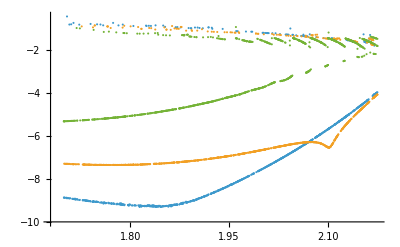

```mathematica
ListPlot[{Extract[data13,{;;,{3,-1}}],Extract[data10,{;;,{3,-1}}],Extract[data,{;;,{3,-1}}]},ScalingFunctions->{"Log10","Log10"}]
```

```mathematica
plots={};
Module[{iy,l,s,point},
Do[iy=-2;l=Extract[label,{{ix},{iy}}];s=Extract[scale,{{ix},{iy}}];
point={Extract[data,{;;,{ix,iy}}],Extract[accept,{;;,{ix,iy}}],Extract[reject,{;;,{ix,iy}}]};
AppendTo[plots,ListPlot[point,AxesLabel->l,ScalingFunctions->s,PlotRange->All]],
{ix,3}]];
```

```mathematica
GraphicsGrid[{plots},PlotRange->All]
```

-Graphics-

```mathematica
Module[{index,l,s,point},
index={1,2,-1};l=Extract[label,{{1},{2},{-1}}];s=Extract[scale,{{1},{2},{-1}}];
point={Extract[data,{;;,index}],Extract[accept,{;;,index}],Extract[reject,{;;,index}]};
P3D=ListPointPlot3D[point,AxesLabel->l,ScalingFunctions->s]];

𝕔={0.5,0.5,0.5};𝕣=3;
Animate[Show[P3D,ViewVector->{Scaled[𝕔+𝕣{Cos[f]Sin[t],Sin[f]Sin[t],Cos[t]}],Scaled[𝕔]}],{f,0,π/2},{t,π/2,0},AnimationRunning->False]
```

#### “Schw_emidRdI_O10_1.m”

```mathematica
Print["ϵ_(min/max) = ",{Min[data[[;;,1]]],Max[data[[;;,1]]]},
"\t μ_(min/max) = ",{Min[data[[;;,2]]],Max[data[[;;,2]]]},
"\t ι_(min/max) = ",{Min[data[[;;,3]]],Max[data[[;;,3]]]}];
```

ϵ_(min/max) = {1.00058×10^-8,9.90488×10^-7}	 μ_(min/max) = {5.00261,19.991}	 ι_(min/max) = {30.0116,179.967}

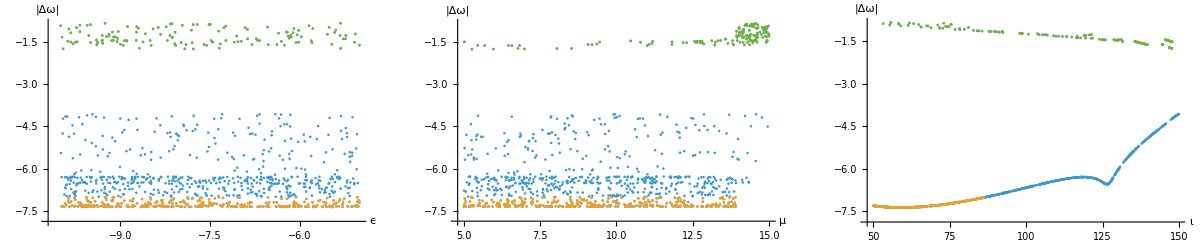

```mathematica
GraphicsGrid[{plots},ImageSize->Full]
```

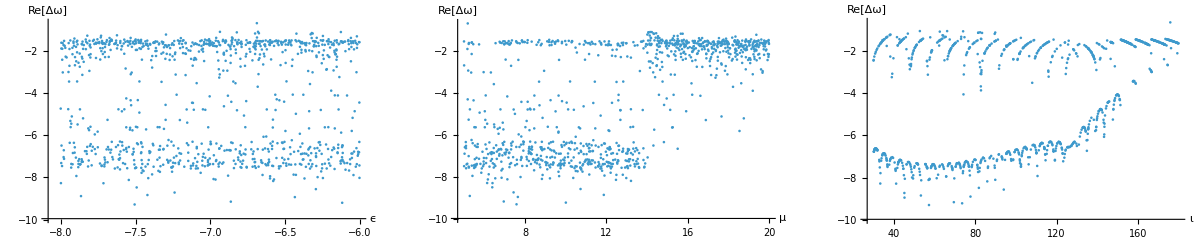

```mathematica
plots=MultiPlot[{data,accept,reject},-2,3];
GraphicsGrid[{plots},ImageSize->Full]
```

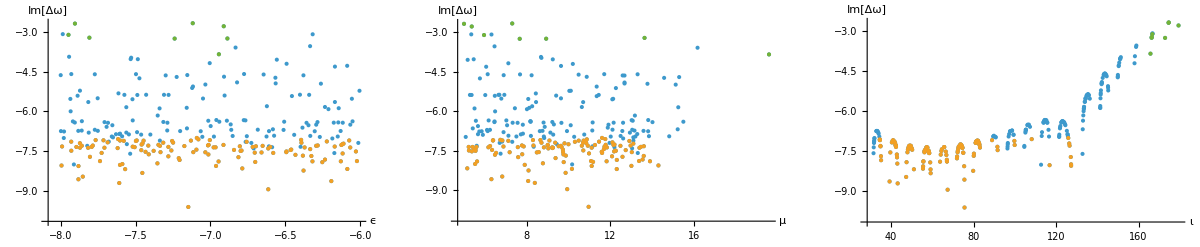

```mathematica
plots=MultiPlot[{data,accept,reject},-1,3];
GraphicsGrid[{plots},ImageSize->Full]
```

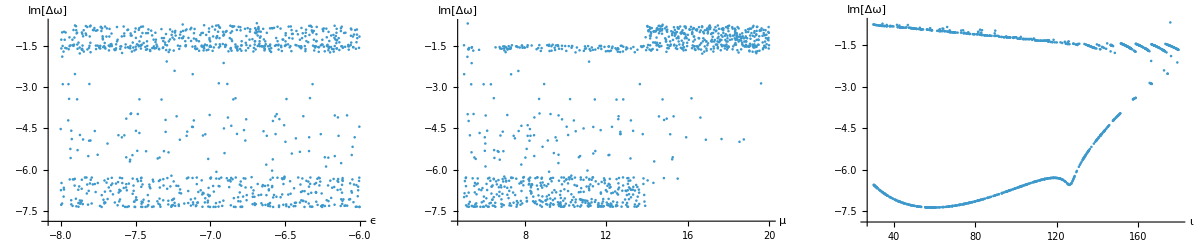

```mathematica
absdev=data[[;;,;;-2]];absdev[[;;,-1]]=Abs[data[[;;,-2]]+data[[;;,-1]]ⅈ];
plots=MultiPlot[{absdev},-1,3];
GraphicsGrid[{plots},ImageSize->Full]
```

#### “Schw_10_emidRdIdA_2.m”

```mathematica
Print["ϵ_(min/max) = ",{Min[data[[;;,1]]],Max[data[[;;,1]]]},
"\t μ_(min/max) = ",{Min[data[[;;,2]]],Max[data[[;;,2]]]},
"\t ι_(min/max) = ",{Min[data[[;;,3]]],Max[data[[;;,3]]]}];
```

ϵ_(min/max) = {1.00234×10^-10,60.}	 μ_(min/max) = {-3.84528×10^-8,-2.1715×10^-8}	 ι_(min/max) = {4.35081×10^-8,4.45467×10^-8}

```mathematica
Join[data[[1,1]],data[[1,2]],{data[[1,3]]}]
```

{9.25119×10^-8,9.59241,60.,-3.77879×10^-8,-2.20887×10^-8,4.37702×10^-8}

```mathematica
plots=MultiPlot[{data,accept,reject},-3,3];
GraphicsGrid[{plots},ImageSize->Full]
```

```mathematica
plots=MultiPlot[{data,accept,reject},-2,3];
GraphicsGrid[{plots},ImageSize->Full]
```

-Graphics-

```mathematica
plots=MultiPlot[{data,accept,reject},-1,3];
GraphicsGrid[{plots},ImageSize->Full]
```

-Graphics-

#### “Schw_10_emodRdIdA_3.m”

```mathematica
Print["ϵ_(min/max) = ",{Min[data[[;;,1]]],Max[data[[;;,1]]]},
"\t μ_(min/max) = ",{Min[data[[;;,2]]],Max[data[[;;,2]]]},
"\t ι_(min/max) = ",{Min[data[[;;,3]]],Max[data[[;;,3]]]}];
```

ϵ_(min/max) = {1.00058×10^-8,9.90488×10^-7}	 μ_(min/max) = {5.00261,19.991}	 ι_(min/max) = {30.0116,179.967}

```mathematica
plots=MultiPlot[{data,accept,reject},-3,3];
GraphicsGrid[{plots},ImageSize->Full]
```

-Graphics-

```mathematica
plots=MultiPlot[{data,accept,reject},-2,3];
GraphicsGrid[{plots},ImageSize->Full]
```

-Graphics-

```mathematica
plots=MultiPlot[{data,accept,reject},-1,3];
GraphicsGrid[{plots},ImageSize->Full]
```

-Graphics-

#### “QNM_Schw_emiod_10_4.m”

```mathematica
Print["ϵ_(min/max) = ",{Min[data[[;;,1]]],Max[data[[;;,1]]]},
"\t μ_(min/max) = ",{Min[data[[;;,2]]],Max[data[[;;,2]]]},
"\t ι_(min/max) = ",{Min[data[[;;,3]]],Max[data[[;;,3]]]}];
```

ϵ_(min/max) = {1.02233×10^-7,0.000978295}	 μ_(min/max) = {5.00197,14.9965}	 ι_(min/max) = {60,60}

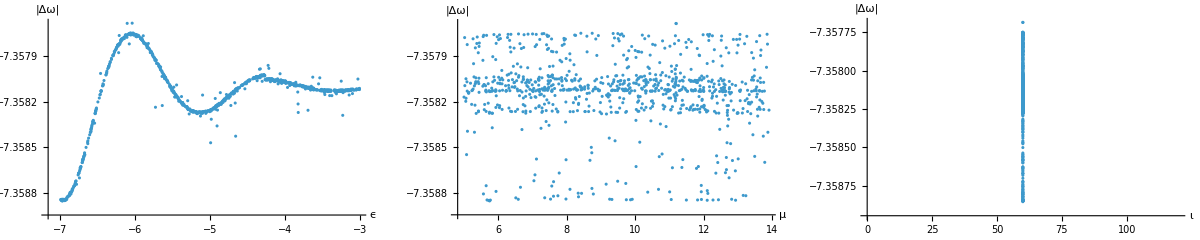

```mathematica
GraphicsGrid[{plots},ImageSize->Full]
```

#### “QNM_Schw_emiod_10_5.m”

```mathematica
Print["ϵ_(min/max) = ",{Min[data[[;;,1]]],Max[data[[;;,1]]]},
"\t μ_(min/max) = ",{Min[data[[;;,2]]],Max[data[[;;,2]]]},
"\t ι_(min/max) = ",{Min[data[[;;,3]]],Max[data[[;;,3]]]}];
```

ϵ_(min/max) = {1/10000000,1/10000000}	 μ_(min/max) = {5.00869,14.9894}	 ι_(min/max) = {60,60}

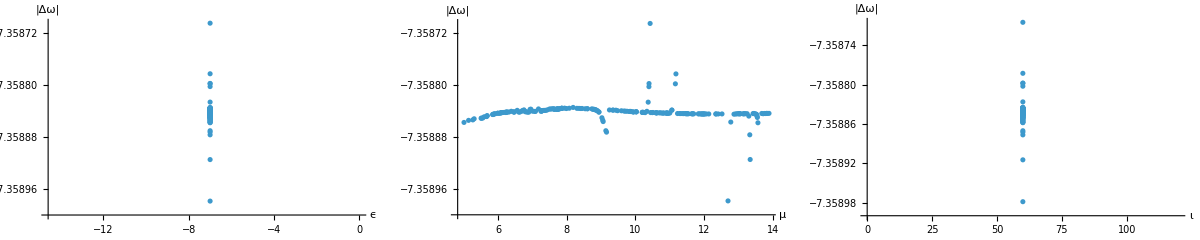

```mathematica
GraphicsGrid[{plots},ImageSize->Full]
```

### Expansion order (ordHor, ordInf)

```mathematica
(* Old version *)
Δroot=Table[FindQNM[ωguess,expHor[[i]],expInf[[i]]][[1]]-ωtrue,{i,1,Length[expHor]}](* deviation from the true value *)
```

{(0.37405620363376538512-0.089242634150749545214 ⅈ)-ωtrue,(0.37366811018861254215-0.088956015402466350852 ⅈ)-ωtrue,(0.3736717875955766716-0.088962502966972786402 ⅈ)-ωtrue,(0.37367167902923969473-0.088962307308522728654 ⅈ)-ωtrue,(0.37367168490111991877-0.088962316156939377181 ⅈ)-ωtrue,(0.37367168441379203617-0.088962315614506840385 ⅈ)-ωtrue}

#### Computation

```mathematica
expHor=Table[CoefHor[i][[1]],{i,5,15,2}];Export["SeriesCoef\\CoefHor_Schw_5_15.m",expHor];
```

```mathematica
expInf=Table[CoefInf[i][[1]],{i,5,15,2}];Export["SeriesCoef\\CoefInf_Schw_5_15.m",expInf];
```

```mathematica
expHor=Import["SeriesCoef\\CoefHor_Schw_5_15.m"];
expInf=Import["SeriesCoef\\CoefInf_Schw_5_15.m"];
```

```mathematica
(* Adapting the finder's input to suite the analysis *)
FindQNM[ωguess_,coefHor_,coefInf_]:=Module[{g,ωroot},
g[x_?NumericQ]:=IntQNM[x,{2,10^-5,10,60}(* based on the previous section *),coefHor,coefInf][[1]];
ωroot=x/.FindRoot[g[x]==0,{x,ωguess},AccuracyGoal->6,WorkingPrecision->20][[1]];
Return[{ωroot,Abs[g[root]]}];
]
```

```mathematica
data=Table[{},{i,expHor},{j,expInf}];

Monitor[Do[Do[ωfound=FindQNM[ωguess,expHor[[i]],expInf[[j]]][[1]];
data[[i,j]]={Length[expHor[[i]]],Length[expInf[[j]]],ωfound,Abs[ωfound-ωSBH]},{j,1,Length[expInf]}],
{i,1,Length[expHor]}],Row[{"ij = ",{i,j}}]];

data//Dimensions
```

{6,6,4}

```mathematica
Export["QNM_data\\QNM_Schw_OdRdI_1.m",data];Clear[data];
```

#### Plots

```mathematica
data=Import["QNM_data\\QNM_Schw_Ood_1.m"];
label={"o_Hor","o_Inf","ω","|Δω|"};scale={None,None,None,"Log10"};
Print["Dim[data] = ",data//Dimensions];
```

Dim[data] = {6,6,4}

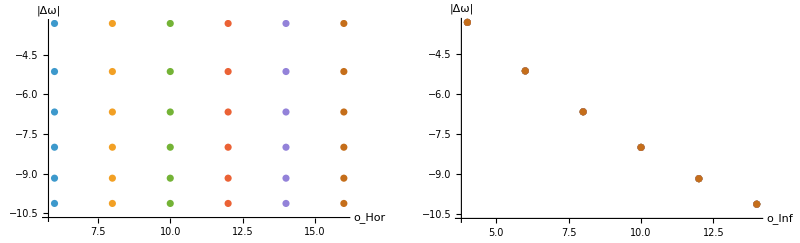

```mathematica
plots={};
Module[{index,l,s,point},
Do[index={i,-1};l=Extract[label,{{i},{-1}}];s=Extract[scale,{{i},{-1}}];
point=Extract[data,{;;,;;,index}];
AppendTo[plots,ListPlot[point,AxesLabel->l,ScalingFunctions->s,PlotRange->All]],
{i,2}]];

GraphicsGrid[{plots},ImageSize->Full]
```